## Collagen Numerical Eigensystems Analysis

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["./results/Parameters","Grid"]
```

/homes/ht/Workspace/collagen_analytical

| 
L: | 5.
m: | 10
N: | 2
kappa: | 1.
sigma: | 1.
Delta: | 0.25
 | 
Extension Minimum: | 0
Extension Maximum: | 20
 | 
 | 
beta: | 4.
mu: | 6.
c: | 4.58
delta: | 19.17
b: | 2.14
k: | 1.57
ev0: | 0.81
C0: | 0.55

Results of calculated Eigenvectors using GSL C++

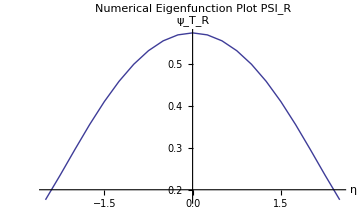
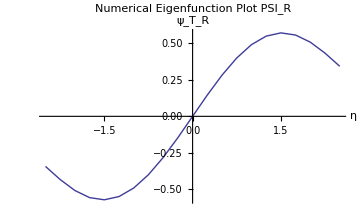
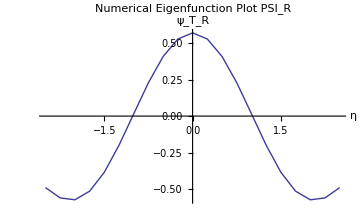
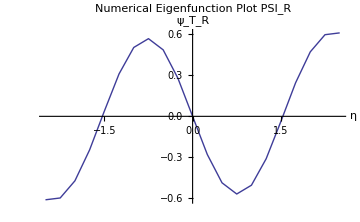

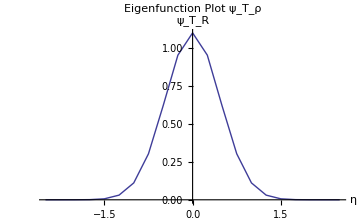
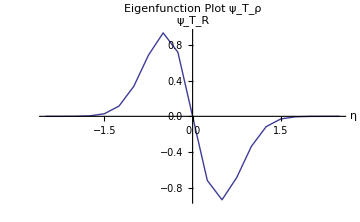
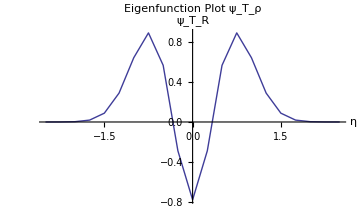
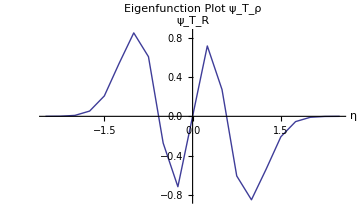

```mathematica
TR0=Import["./logs/TR/Phi_r_0.TR","Table"];
TR1=Import["./logs/TR/Phi_r_1.TR","Table"];
TR2=Import["./logs/TR/Phi_r_2.TR","Table"];
TR3=Import["./logs/TR/Phi_r_3.TR","Table"];
TR4=Import["./logs/TR/Phi_r_4.TR","Table"];
TR5=Import["./logs/TR/Phi_r_5.TR","Table"];

{ListLinePlot[{TR0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{TR3},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Numerical Eigenfunction Plot PSI_R",ImageSize->Medium]}

Tρ0=Import["./logs/TROE/Phi_roe_0.TROE","Table"];
Tρ1=Import["./logs/TROE/Phi_roe_1.TROE","Table"];
Tρ2=Import["./logs/TROE/Phi_roe_2.TROE","Table"];
Tρ3=Import["./logs/TROE/Phi_roe_3.TROE","Table"];
Tρ4=Import["./logs/TROE/Phi_roe_4.TROE","Table"];
Tρ5=Import["./logs/TROE/Phi_roe_5.TROE","Table"];

{ListLinePlot[{Tρ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ3},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_ρ",ImageSize->Medium]}

Tλ0=Import["./logs/TLAMBDA/Phi_lambda_0.TLAMBDA","Table"];
Tλ1=Import["./logs/TLAMBDA/Phi_lambda_1.TLAMBDA","Table"];
Tλ2=Import["./logs/TLAMBDA/Phi_lambda_2.TLAMBDA","Table"];
Tλ3=Import["./logs/TLAMBDA/Phi_lambda_3.TLAMBDA","Table"];
Tλ4=Import["./logs/TLAMBDA/Phi_lambda_4.TLAMBDA","Table"];
Tλ5=Import["./logs/TLAMBDA/Phi_lambda_5.TLAMBDA","Table"];

{ListLinePlot[{Tλ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ3},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Eigenfunction Plot ψ_T_λ",ImageSize->Medium]}

R0A=Import["./logs/R_Analytical/PSI_R_0.RA","Table"];
R1A=Import["./logs/R_Analytical/PSI_R_1.RA","Table"];
R2A=Import["./logs/R_Analytical/PSI_R_2.RA","Table"];
R3A=Import["./logs/R_Analytical/PSI_R_3.RA","Table"];
R4A=Import["./logs/R_Analytical/PSI_R_4.RA","Table"];
R5A=Import["./logs/R_Analytical/PSI_R_5.RA","Table"];

{ListLinePlot[{R0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{R1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{R2A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium],
ListLinePlot[{R3A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, R]]},PlotLabel->"Analytical Eigenfunction Plot PSI_R",ImageSize->Medium]}

Tρ0A=Import["./logs/ROE_Analytical/PSI_ROE_0.ROEA","Table"];
Tρ1A=Import["./logs/ROE_Analytical/PSI_ROE_1.ROEA","Table"];
Tρ2A=Import["./logs/ROE_Analytical/PSI_ROE_2.ROEA","Table"];
Tρ3A=Import["./logs/ROE_Analytical/PSI_ROE_3.ROEA","Table"];
Tρ4A=Import["./logs/ROE_Analytical/PSI_ROE_4.ROEA","Table"];
Tρ5A=Import["./logs/ROE_Analytical/PSI_ROE_5.ROEA","Table"];

Tλ0A=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_0.LAMBDAA","Table"];
Tλ1A=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_1.LAMBDAA","Table"];
Tλ2A=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_2.LAMBDAA","Table"];
Tλ3A=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_3.LAMBDAA","Table"];
Tλ4A=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_4.LAMBDAA","Table"];
Tλ5A=Import["./logs/LAMBDA_Analytical/PSI_LAMBDA_5.LAMBDAA","Table"];

{ListLinePlot[{Tρ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρ]]},PlotLabel->"Eigenfunction Numerical C++ Plot of ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρ]]},PlotLabel->"Eigenfunction Analytical C++ Plot of ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ0,Tρ0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρ]]},PlotLabel->"Comparison Plot of ψ_T_ρ",ImageSize->Medium]}

{ListLinePlot[{Tρ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρ]]},PlotLabel->"Eigenfunction Numerical C++ Plot of ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρ]]},PlotLabel->"Eigenfunction Analytical C++ Plot of ψ_T_ρ",ImageSize->Medium],
ListLinePlot[{Tρ1,Tρ1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, Subscript[T, ρ]]},PlotLabel->"Comparison Plot of ψ_T_ρ",ImageSize->Medium]}

{ListLinePlot[{Tλ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, "T_λ"]},PlotLabel->"Eigenfunction Numerical C++ Plot of ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, "T_λ"]},PlotLabel->"Eigenfunction Analytical C++ Plot of ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ0,Tλ0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, "T_λ"]},PlotLabel->"Comparison Plot of ψ_T_λ",ImageSize->Medium]}

{ListLinePlot[{Tλ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, "T_λ"]},PlotLabel->"Eigenfunction Numerical C++ Plot of ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, "T_λ"]},PlotLabel->"Eigenfunction Analytical C++ Plot of ψ_T_λ",ImageSize->Medium],
ListLinePlot[{Tλ1,Tλ1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, Subscript[ψ, "T_λ"]},PlotLabel->"Comparison Plot of ψ_T_λ",ImageSize->Medium]}
```

Analytical Calculation of Eigenfunctions (Mathematica)

### Constants

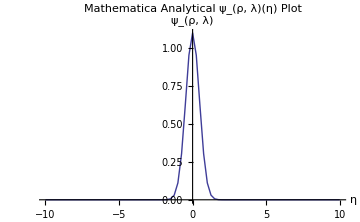
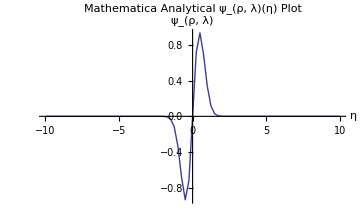
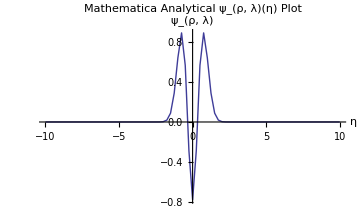
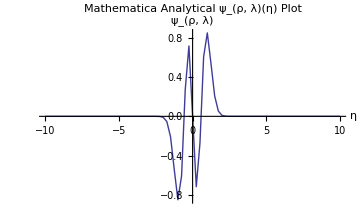

Normalisation of Eigenfunctions Ψ_1,Ψ_2,Ψ_3

Ψ_1)Integral Normalisation ∫_(-∞)^∞ Conjugate[Ψ[0,η]]Ψ[0,η]ⅆη:

1.

Ψ_1)Discrete Normalisation ∑_(i = -m)^m Ψ[0,iΔ]Ψ[0,iΔ]Δ:

1.

Ψ_2)Integral Normalisation ∫_(-∞)^∞ Conjugate[Ψ[1,η]]Ψ[1,η]ⅆη:

1.

Ψ_2)Discrete Normalisation ∑_(i = -m)^m Ψ[1,iΔ]Ψ[1,iΔ]Δ:

1.

Ψ_3)Integral Normalisation ∫_(-∞)^∞ Conjugate[Ψ[2,η]]Ψ[2,η]ⅆη:

1.

Ψ_3)Discrete Normalisation ∑_(i = -m)^m Ψ[2,iΔ]Ψ[2,iΔ]Δ:

1.

```mathematica
L = 5;
m = 10;

n = 2;
σ = 1;
κ  = 1;

Δ = L/(2m);

u = 0;

β=4;
μ=(6 σ)/κ//N;
c=((μ^2+2 β μ)^(1/2))/2//N;
δ=2 c+μ+β;
b=1/2((δ^2-β^2)/δ)^(1/2)//N;
k=Log[δ/β]//N;
Subscript[e, 0]=((4 π)/δ)^(1/2)//N;
Subscript[E, 00][h_]:=Subscript[e, 0]*Exp[-k h];
Subscript[C, 0]=1/2 ((2 π)/((μ^2+2 β μ)^(1/2)))^(-1/4);
nC[n_]:=(1/(2^n Factorial[n]))^(1/2);
Ψ[n_,η_]:=2 Subscript[C, 0] nC[n] HermiteH[n,b η] Exp[-(c η^2)/2];

AnalyticalT00Data0=Table[{i,Ψ[0,i]},{i,-m,m,Δ}];
AnalyticalT00Data1=Table[{i,Ψ[1,i]},{i,-m,m,Δ}];
AnalyticalT00Data2=Table[{i,Ψ[2,i]},{i,-m,m,Δ}];
AnalyticalT00Data3=Table[{i,Ψ[3,i]},{i,-m,m,Δ}];

{ListLinePlot[{AnalyticalT00Data0},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}],
ListLinePlot[{AnalyticalT00Data1},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}],
ListLinePlot[{AnalyticalT00Data2},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}],
ListLinePlot[{AnalyticalT00Data3},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}]}

Print["Normalisation of Eigenfunctions Ψ_1,Ψ_2,Ψ_3"]
Print["\nΨ_1)Integral Normalisation ∫_(-∞)^∞ Conjugate[Ψ[0,η]]Ψ[0,η]ⅆη:"]
 ∫_(-∞)^∞ Ψ[0,η]Ψ[0,η]ⅆη
Print["Ψ_1)Discrete Normalisation ∑_(i = -m)^m Ψ[0,iΔ]Ψ[0,iΔ]Δ:"]
∑_(i=-m)^m Ψ[0,i Δ]Ψ[0,i Δ]Δ
Print["\nΨ_2)Integral Normalisation ∫_(-∞)^∞ Conjugate[Ψ[1,η]]Ψ[1,η]ⅆη:"]
 ∫_(-∞)^∞ Ψ[1,η]Ψ[1,η]ⅆη
Print["Ψ_2)Discrete Normalisation ∑_(i = -m)^m Ψ[1,iΔ]Ψ[1,iΔ]Δ:"]
∑_(i=-m)^m Ψ[1,i Δ]Ψ[1,i Δ]Δ
Print["\nΨ_3)Integral Normalisation ∫_(-∞)^∞ Conjugate[Ψ[2,η]]Ψ[2,η]ⅆη:"]
 ∫_(-∞)^∞ Ψ[2,η]Ψ[2,η]ⅆη
Print["Ψ_3)Discrete Normalisation ∑_(i = -m)^m Ψ[2,iΔ]Ψ[2,iΔ]Δ:"]
∑_(i=-m)^m Ψ[2,i Δ]Ψ[2,i Δ]Δ
```

Numerical Calculation of Eigenfunctions (Mathematica)

Functions & Eigensystem Calculation

```mathematica
V[η_] := 1/2(σ η^2)/κ;
T[ξ1_, ξ2_] := Exp[-(ξ1 - ξ2)^2];
T̂[ η1_, η2_] :=   Exp[-(η1 - η2)^2]* Exp[-3(V[η1] + V[η2])];

MT = Table[Chop[Δ T[ Δ ξ1, Δ ξ2]],{ξ1, -m, m}, {ξ2, -m, m}] // N;
Subscript[MT, ρ] = Table[ Chop[Δ T̂[Δ η1, Δ η2]], {η1, -m,m}, {η2, -m, m}] // N;
Subscript[MT, λ] = Table[ Chop[Δ T̂[Δ η1, Δ η2]], {η1, -m,m}, {η2, -m, m}] // N;

dataMT = Flatten[ Table[{Δ (i - (m + 1)), Δ (j - (m + 1)),MT[[i, j]]}, {i, 1, (2 m + 1)}, {j, 1, (2 m + 1)}], 1] // N;
Subscript[dataMT, ρ] =Flatten[Table[{Δ (i - (m + 1)), Δ (j - (m + 1)),Subscript[MT, ρ][[i, j]]}, {i, 1, (2 m + 1)}, {j, 1, (2 m + 1)}],1] // N;
Subscript[dataMT, λ] =Flatten[Table[{Δ (i - (m + 1)), Δ (j - (m + 1)),Subscript[MT, λ][[i, j]]}, {i, 1, (2 m + 1)}, {j, 1, (2 m + 1)}],1] // N;

λ = Eigenvalues[MT];
Subscript[λ̂, ρ] = Eigenvalues[Subscript[MT, ρ]];
Subscript[λ̂, λ] = Eigenvalues[Subscript[MT, λ]];

Subscript[ψ, r] = Δ^(-1/2)Eigenvectors[MT];
Subscript[ψ, ρ] =  Δ^(-1/2)Eigenvectors[Subscript[MT, ρ]];
Subscript[ψ, λ] =  Δ^(-1/2)Eigenvectors[Subscript[MT, λ]];

Print["Normalisation test for Mathematica Numerical Eigenfunctions Ψ_1,Ψ_2,Ψ_3"]
Print["ψ_r)Discrete Normalisation ∑_(i = -m)^m ψ_r[1,i+(m+1)]ψ_r[1,i+(m+1)]Δ:"]
∑_(i=-m)^m Subscript[ψ, r][[1,i+(m+1)]]Subscript[ψ, r][[1,i+(m+1)]]Δ
Print["ψ_ρ)Discrete Normalisation ∑_(i = -m)^m ψ_ρ[1,i+(m+1)]ψ_ρ[1,i+(m+1)]Δ:"]
∑_(i=-m)^m Subscript[ψ, ρ][[1,i+(m+1)]]Subscript[ψ, ρ][[1,i+(m+1)]]Δ
Print["ψ_λ)Discrete Normalisation ∑_(i = -m)^m ψ_λ[1,i+(m+1)]ψ_λ[1,i+(m+1)]Δ:"]
∑_(i=-m)^m Subscript[ψ, λ][[1,i+(m+1)]]Subscript[ψ, λ][[1,i+(m+1)]]Δ
```

Normalisation test for Mathematica Numerical Eigenfunctions Ψ_1,Ψ_2,Ψ_3

ψ_r)Discrete Normalisation ∑_(i = -m)^m ψ_r[1,i+(m+1)]ψ_r[1,i+(m+1)]Δ:

1.

ψ_ρ)Discrete Normalisation ∑_(i = -m)^m ψ_ρ[1,i+(m+1)]ψ_ρ[1,i+(m+1)]Δ:

1.

ψ_λ)Discrete Normalisation ∑_(i = -m)^m ψ_λ[1,i+(m+1)]ψ_λ[1,i+(m+1)]Δ:

1.

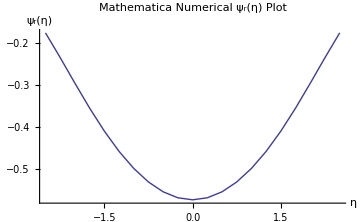
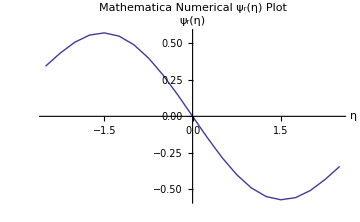
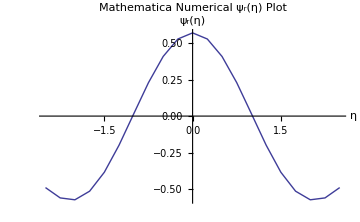
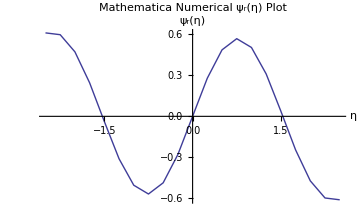

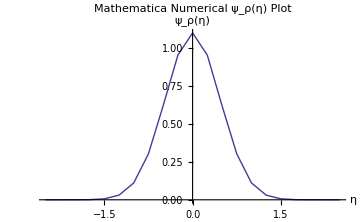
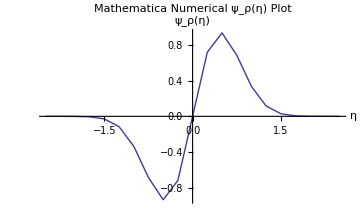
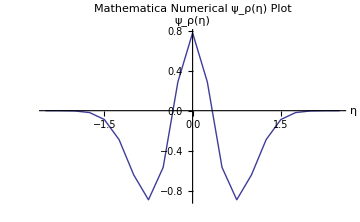
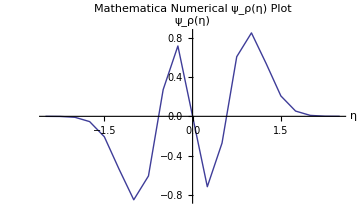

```mathematica
data0r = Table[{Δ (i - (m + 1)),Subscript[ψ, r][[1, i]]}, {i,1, (2 m + 1)}] // N;
data1r = Table[{Δ (i - (m + 1)),Subscript[ψ, r][[2, i]]}, {i,1, (2 m + 1)}] // N;
data2r = Table[{Δ (i - (m + 1)),Subscript[ψ, r][[3, i]]}, {i,1, (2 m + 1)}] // N;
data3r = Table[{Δ (i - (m + 1)),Subscript[ψ, r][[4, i]]}, {i,1, (2 m + 1)}] // N;

data0ρ = Table[{Δ (i - (m + 1)),Subscript[ψ, ρ][[1, i]]}, {i,1, (2 m + 1)}] // N;
data1ρ = Table[{Δ (i - (m + 1)),Subscript[ψ, ρ][[2, i]]}, {i,1, (2 m + 1)}] // N;
data2ρ = Table[{Δ (i - (m + 1)),Subscript[ψ, ρ][[3, i]]}, {i,1, (2 m + 1)}] // N;
data3ρ = Table[{Δ (i - (m + 1)),Subscript[ψ, ρ][[4, i]]}, {i,1, (2 m + 1)}] // N;

data0λ = Table[{Δ (i - (m + 1)),Subscript[ψ, λ][[1, i]]}, {i,1, (2 m + 1)}] // N;
data1λ = Table[{Δ (i - (m + 1)),Subscript[ψ, λ][[2, i]]}, {i,1, (2 m + 1)}] // N;
data2λ = Table[{Δ (i - (m + 1)),Subscript[ψ, λ][[3, i]]}, {i,1, (2 m + 1)}] // N;
data3λ = Table[{Δ (i - (m + 1)),Subscript[ψ, λ][[4, i]]}, {i,1, (2 m + 1)}] // N;


{ListLinePlot[data0r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_r(η)  Plot", AxesLabel -> {η, "ψ_r(η)"}],
ListLinePlot[data1r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_r(η)  Plot", AxesLabel -> {η, "ψ_r(η)"}],
ListLinePlot[data2r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_r(η)  Plot",AxesLabel -> {η, "ψ_r(η)"}],
ListLinePlot[data3r,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_r(η)  Plot",AxesLabel -> {η, "ψ_r(η)"}]}

{ListLinePlot[data0ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot", AxesLabel -> {η, "ψ_ρ(η)"}],
ListLinePlot[data1ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot", AxesLabel -> {η, "ψ_ρ(η)"}],
ListLinePlot[data2ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot",AxesLabel -> {η, "ψ_ρ(η)"}],
ListLinePlot[data3ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot",AxesLabel -> {η, "ψ_ρ(η)"}]}

{ListLinePlot[data0λ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_λ(η)  Plot", AxesLabel -> {η, "ψ_λ(η)"}],
ListLinePlot[data1λ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_λ(η)  Plot", AxesLabel -> {η, "ψ_λ(η)"}],
ListLinePlot[data2λ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_λ(η)  Plot",AxesLabel -> {η, "ψ_λ(η)"}],
ListLinePlot[data3λ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All, PlotLabel->"Mathematica  Numerical  ψ_λ(η)  Plot",AxesLabel -> {η, "ψ_λ(η)"}]}
```

Comparasion of ψ_(ρ,λ) Eigenfunctions

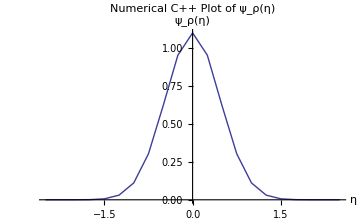
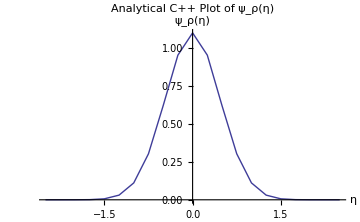
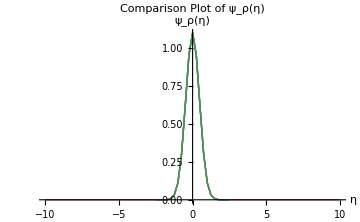
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

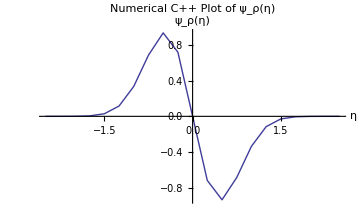
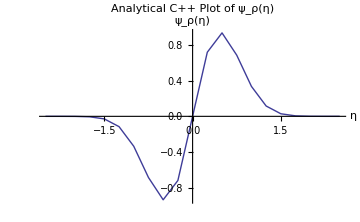
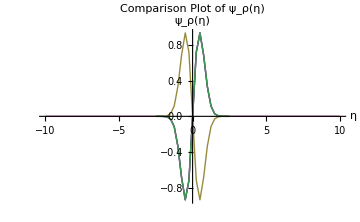
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

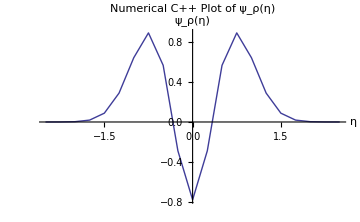
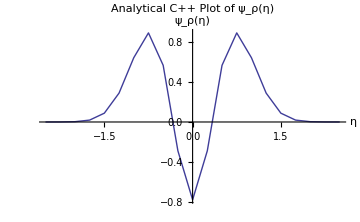
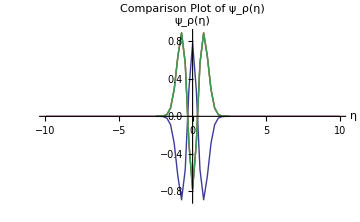
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListLinePlot[data0ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot", AxesLabel -> {η, "ψ_ρ(η)"}],
ListLinePlot[{AnalyticalT00Data0},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}],
ListLinePlot[{Tρ0},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Numerical C++ Plot of ψ_ρ(η)",ImageSize->Medium],
ListLinePlot[{Tρ0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Analytical C++ Plot of ψ_ρ(η)",ImageSize->Medium],
ListLinePlot[{data0ρ,AnalyticalT00Data0,Tρ0,Tρ0A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Comparison Plot of ψ_ρ(η)",ImageSize->Medium]}

{ListLinePlot[data1ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot", AxesLabel -> {η, "ψ_ρ(η)"}],
ListLinePlot[{AnalyticalT00Data1},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}],
ListLinePlot[{Tρ1},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Numerical C++ Plot of ψ_ρ(η)",ImageSize->Medium],
ListLinePlot[{Tρ1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Analytical C++ Plot of ψ_ρ(η)",ImageSize->Medium],
ListLinePlot[{data1ρ,AnalyticalT00Data1,Tρ1,Tρ1A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Comparison Plot of ψ_ρ(η)",ImageSize->Medium]}

{ListLinePlot[data2ρ,PlotStyle->{Thick},  ImageSize -> Medium, AxesOrigin -> {0, 0}, PlotRange -> All,PlotLabel->"Mathematica  Numerical  ψ_ρ(η)  Plot", AxesLabel -> {η, "ψ_ρ(η)"}],
ListLinePlot[{AnalyticalT00Data2},PlotRange->All,PlotStyle->{Thick},ImageSize->Medium,PlotLabel->"Mathematica  Analytical  ψ_(ρ, λ)(η)  Plot",AxesLabel -> {η, "ψ_(ρ, λ)"}],
ListLinePlot[{Tρ2},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Numerical C++ Plot of ψ_ρ(η)",ImageSize->Medium],
ListLinePlot[{Tρ2A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Analytical C++ Plot of ψ_ρ(η)",ImageSize->Medium],
ListLinePlot[{data2ρ,AnalyticalT00Data2,Tρ2,Tρ2A},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {η, "ψ_ρ(η)"},PlotLabel->"Comparison Plot of ψ_ρ(η)",ImageSize->Medium]}
```